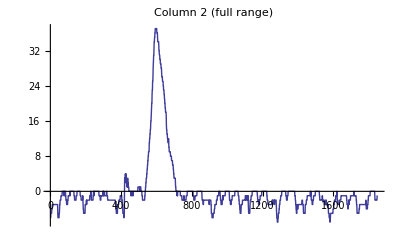
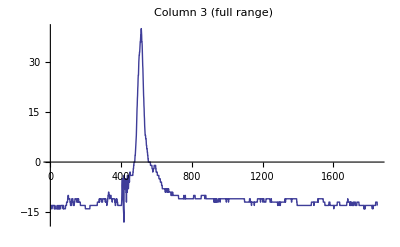
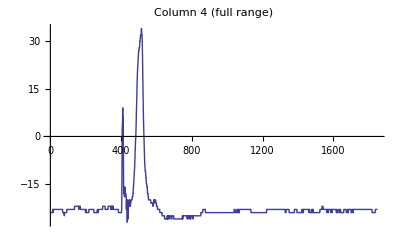
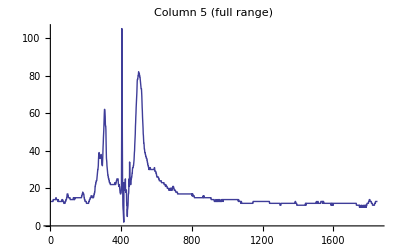
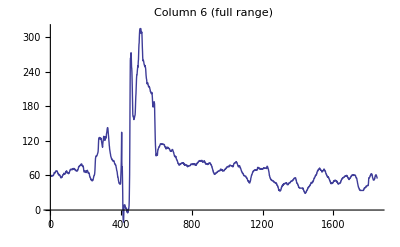
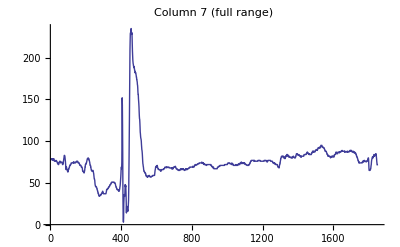
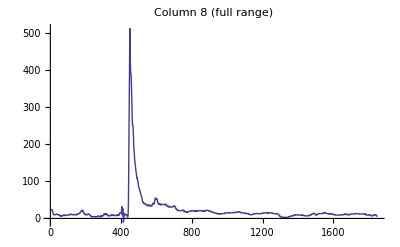
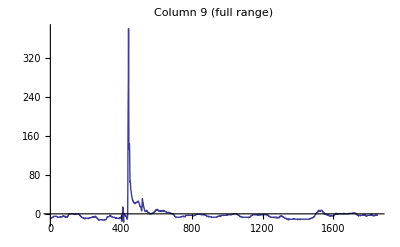

```mathematica
ClearAll[file,x]
(*file=(Import["P:/mhh/00506534.ASC.csv.head.csv","Data","HeaderLines"->0]);*)
file=(Import["M:\\Proband1\\00506534Schluck7.ASC.data\\data.csv","Data","HeaderLines"->0]);


ParallelTable[ListPlot[file[[All,x]],PlotLabel->StringJoin["Column ",ToString[x], " (full range)"], Joined->True,PlotRange->All],{x,2,28}]
ParallelTable[ListPlot[file[[All,x]],PlotLabel->StringJoin["Column ",ToString[x]], Joined->True],{x,2,28}]
```